List of distances with number of occurances:

{{1,47},{√3,9},{√(1/6 (9+√33)),15},{√(1/6 (9-√33)),18},{√(1/6 (7-√33)),16},{√(2-√(11/3)),16},{√(5/3),15},{1/(√3),23},{√(1/3 (10-√33)),3},{√(1/6 (7+√33)),11},{√(1/6 (29-5 √33)),1},{2/(√3),11},{√(1/3 (8-√33)),8},{√(1/6 (15-√33)),11},{√(1/2 (7-√33)),7},{√(1/3 (10+√33)),2},{√(2+√(11/3)),8},{√(1/6 (15+√33)),8},{√(7/3),8},{√5,1},{√(1/3 (8+√33)),3},{√(4-√(11/3)),3},{√(1/2 (9-√33)),3},{√(1/3 (16-√33)),1},{√(5/6 (7-√33)),1},{√(1/6 (19-3 √33)),3},{√(5-2 √(11/3)),1}}

Number of distinct distances:

27

Plot of the unit distance graph on vertex set:

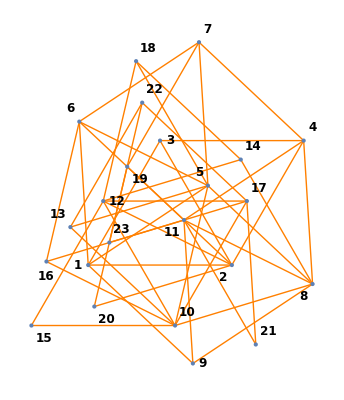

{{w_0,1},{w_T,1},{w_1,1},{w_2,26},{w_C,2321}}

Number of congruence constraints:

2321

All the listed congruences are formally checked:

True

Number of all atoms:

8388608

Number of independent atoms:

13552

Calculating the value of nu.

Running over independent atoms:

The value of maximal error:

6.71224×10^-8

nu = 0.000001 works.

Function fi[t] plotted on [0,50]

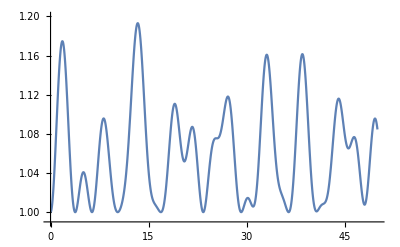

Function fi[t] plotted on [0,3000]

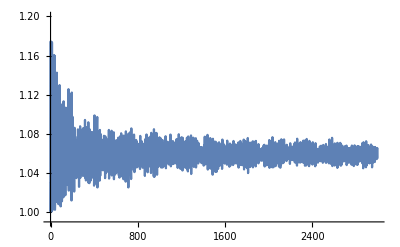

w1(1), the limit of fi[t] as t-> infinity:

1.05938

Sum of w0 plus the sum of the absolute values of w2 coefficients:

1.93062

Last local maximum of the 0th Bessel function on [0,1000]

{0.0252337,{t→999.811}}

Value of w_1 - 2 J0(s_0)

1.00892

Interval arithmetic for estimating f

On the interval [1000, 10000]:

Derivative on the interval [1000, 10000]

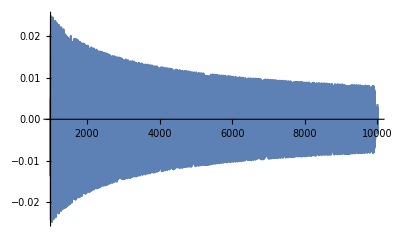

Maximum of abs. value of derivative on the interval [1000, 10000]

{0.0252139,{t→1001.38}}

Derivative is less than 0.03

Minimal value of fi[t] with t*eps \in [1000,10000], eps=1

1.03829

Minimum is larger than 1.03, OK

On the interval [100, 1000]:

Derivative on the interval [100, 10000]

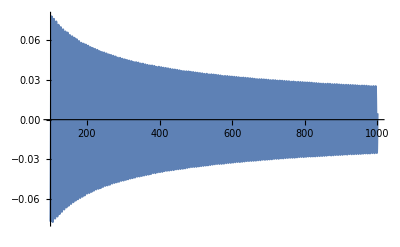

Maximum of abs. value of derivative on the interval [100, 1000]

{0.0771454,{t→100.}}

Derivative less than 0.1

Minimal value of fi[t] with t*eps \in [100,1000], eps=0.1

1.01102

Minimum is larger than 1.01, OK

On the interval [0, 100]:

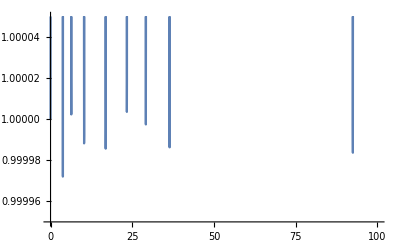

Derivative on the interval [0, 100]

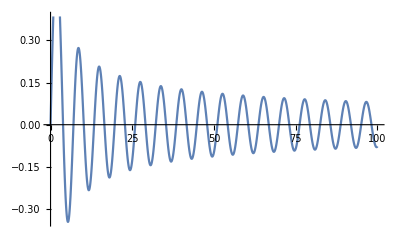

Maximum of abs. value of derivative on the interval [100, 1000]

{0.581865,{t→1.84118}}

Derivative less than 1.

Finding local minima starting from points t*eps in [0,100] with eps=0.1

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

Smallest local minimum:

{0.99995,{t→3.77488}}

Value of difference from 1

0.000049969

mu = 0.00006 works

0.00006

Checking the value of mu by interval arithmetic.

Number of points in [0,100] of the form k*eps with mu=0.001 with  fi[k*mu]<0.99995+mu

2629

Checking on the intervals of length 2 mu around these points with fine interval arithmetic, using eps=0.00001

Maximal total error:

0.000059969

The value of nu

1.×10^-6

The value of mu

0.00006

Upper estimate for density

0.246988

```mathematica
(* path of the .csv file containing the data. Normally it is in the same directory as the Mathematica notebook.  *)
SetDirectory[NotebookDirectory[]];
path="g23.csv";

(* Defining the vertices of the graph G_{23}*)

n = 23;

X={0,
1,
1/2+(1/2)*3^(1/2)*I,
3/2+(1/2)*3^(1/2)*I,
5/6+(1/6)*11^(1/2)*I,
-1/12*33^(1/2)+5/12+(1/12)*11^(1/2)*I+(5/12)*3^(1/2)*I,
-1/12*33^(1/2)+5/4+(5/12)*3^(1/2)*I+(1/4)*11^(1/2)*I,
(1/12)*33^(1/2)+13/12-1/12*11^(1/2)*I+(1/12)*3^(1/2)*I,
1/4+(1/12)*33^(1/2)-1/4*11^(1/2)*I+(1/12)*3^(1/2)*I,
-1/12*33^(1/2)+13/12-1/12*11^(1/2)*I-1/12*3^(1/2)*I,
2/3-1/6*11^(1/2)*I+(1/2)*3^(1/2)*I,
-1/12*33^(1/2)+7/12-1/12*11^(1/2)*I+(5/12)*3^(1/2)*I,
-1/6*33^(1/2)+5/6-1/6*3^(1/2)*I+(1/6)*11^(1/2)*I,
(1/12)*33^(1/2)+7/12-1/12*11^(1/2)*I+(7/12)*3^(1/2)*I,
-1/12*33^(1/2)+1/12-1/12*11^(1/2)*I-1/12*3^(1/2)*I,
-1/6*33^(1/2)+2/3-1/6*11^(1/2)*I+(1/3)*3^(1/2)*I,
-1/12*33^(1/2)+19/12-1/12*11^(1/2)*I+(5/12)*3^(1/2)*I,
1/3+(1/6)*11^(1/2)*I+(1/2)*3^(1/2)*I,
-1/12*33^(1/2)+3/4-1/12*3^(1/2)*I+(1/4)*11^(1/2)*I,
-1/6*33^(1/2)+1-1/6*3^(1/2)*I,
7/6-1/6*11^(1/2)*I,
-1/6*33^(1/2)+4/3+(1/6)*11^(1/2)*I+(1/3)*3^(1/2)*I,
-1/4*33^(1/2)+19/12-1/12*11^(1/2)*I+(1/4)*3^(1/2)*I};

(* Table of distances between vertices *)
DX = Table[Simplify[Abs[X[[i]] - X[[j]]]], {i, 1,n}, {j, 1, n}];
DXs = Table[Simplify[Abs[X[[i]] - X[[j]]]], {i, 1,n-1}, {j, i+1, n}];

(* List of distances with number of occurances *)
Print["List of distances with number of occurances:"]
Tally[Flatten[DXs]]
Print["Number of distinct distances:"]
Length[Tally[Flatten[DXs]]]

(* Finding unit distances within X*)
XPairsUnit = {};
For[i=1, i<n, 
For[j = i+1, j<= n, 
If[DX[[i]][[j]]==1, AppendTo[XPairsUnit, {i,j}]];
j++;
];
i++]
LUP=Length[XPairsUnit]; (*number of unit distances *)


(*Drawing X*)
Print["Plot of the unit distance graph on vertex set:"]
pt[x_]:={Re[x], Im[x]};
pl1=ListPlot[Table[Labeled[pt[X[[i]]], i], {i, 1, n}], Axes->False, LabelStyle->Directive[Bold,12], PlotStyle->PointSize[Large]];
edges= Graphics[{Orange, Line[{pt[X[[#[[1]]]]], pt[X[[#[[2]]]]]}]}]&/@XPairsUnit;
Show[Join[ edges, {pl1}]]

(* Importing dual coefficients from external file. Directory needs to be set to the current directory containing the data file! *)
coeffdata= Import[path,"Data"];
coeff = #[[1]] & /@ coeffdata;
coefftype = #[[2]] & /@ coeffdata;

(*Number of non-zero coefficients sorted by type*)
Tally[coefftype]

w2N = Tally[coefftype][[4]][[2]]; (*Number of IE2 constraints*)
wCN = Tally[coefftype][[5]][[2]];(*Number of congruence constraints *)
w0 = coeff[[1]];
wT = coeff[[2]];
w1 = coeff[[3]];
w2 = Take[ coeff,{4, 3 + w2N}];
w2Pairs =  {#[[3]],#[[4]]}  & /@ Take[ coeffdata,{4, 3 + w2N}];
wC = Take[ coeff, {4 + w2N, 3 + w2N + wCN}];

(*Checking congruences*)
(*Extracting index sets of congruences*)
CongI = {};
Index0 = 3 + w2N;
For[i=1, (*i<=wCN, *) i<=wCN,
(*index sets*)
AppendTo[CongI, {ToExpression@StringSplit[ coeffdata[[Index0 + i]][[3]],{",", "{", "}"}],ToExpression@StringSplit[ coeffdata[[Index0 + i]][[4]],{",", "{", "}"}]}];
i++;
]
(*Number of congruence constraints *)
Print["Number of congruence constraints:"]
Length[CongI]
(*Drop congruences of one-element vertex sets, as these are guaranteed to hold *)
CongR = Select[CongI,Length[#[[1]]]>1&];
CongN = Length[CongR];
(*Vertex sets of congruences with at least 2 vertices*)
CongX = {Part[X,#[[1]]],Part[X,#[[2]]]}&/@CongR;
(*Checking that congruences indeed hold. Data is organized so as the congruence keeps the permutation of vertices.*)
CongHolds = True;
Clear[I1, I2]
Print["All the listed congruences are formally checked:"]
For[i=1, i<=CongN, 
Clear[X1, X2, X1T, X2T, X1R, X2R];
X1 = CongX[[i]][[1]];
X2 = CongX[[i]][[2]];
(*Translate vector sets so that first point is origin *)
X1T = #-X1[[1]]&/@X1;
X2T = #-X2[[1]]&/@X2;
(*Rotate vector sets so that second point has argument 0 *)
X1R = #/X1T[[2]]&/@X1T;
X2R = #/X2T[[2]]&/@X2T;
(*Sets are either congruent or the conjugate of the second set is congruent *)
cong = Evaluate[(Simplify[X1R-X2R]==Table[0, Length[X1R]]) ||(Simplify[X1R - Conjugate@X2R] ==Table[0, Length[X1R]] )];
CongHolds = CongHolds && cong;
i++;
]
CongHolds

(*Finding independent atoms*)
Bin[i_]:=IntegerDigits[i, 2,n ]; (*atoms are indexed by 0-1 digits *)
Flat1 = Table[1, n];
VSet[i_]:=Flatten[Position[Bin[i],1],1];  (* vertices in the atom corresponding to number i *)
el[i_,j_]:=Insert[Table[0,{n-2}],1,{{i}, {j-1}}]; (* String with the i-th and j-th coordinate being 1, others 0. Important that i<j.*)
ET = el[#[[1]], #[[2]]]&/@XPairsUnit;  (*Incidence matrix of unit distances within X*)
TransET = Transpose[ET];  (* Transpose of ET *)

IndepAtoms={};
Const1 = Table[1,LUP];
Print["Number of all atoms:"]
2^n
Dynamic[iu]
Print["Number of independent atoms:"]
For[iu=1, iu<=2^n,
If[FirstPosition[Bin[iu].TransET ,2,0]==0, AppendTo[IndepAtoms,iu]];   (* There is no 2 element in the list iff VSet[iu] is independent *)
iu++
];
LengthA=Length[IndepAtoms]



(* Calculating the value of nu *)
eps1 =Join[{1}, Table[0, n-1]] ;

Eps[A_]:= ReplacePart[ConstantArray[0, n], {#}&/@A -> 1]  ;  (*characteristic sign sequence of the vertex set A *) 

w2Eps = Eps/@w2Pairs;
CongEps = {Eps[#[[1]]], Eps[#[[2]]]}&/@CongI;

CongL = Length[#[[1]]]&/@CongI; (*array of lengths of congruences *)

Print["Calculating the value of nu."]
Print["Running over independent atoms:"]
MA = 0;
Dynamic[iA]
For[iA=1,iA<=LengthA, 
eps = Bin[IndepAtoms[[iA]]]; (* index set of the i'th independent atom *)
Meps = wT - w1*(eps.eps1)-  (* eps.eps1 =1 if 1 is in the vertex set of atom no. i, 0 otherwise*)  Sum[eps[[w2Pairs[[j]][[1]]]]* eps[[w2Pairs[[j]][[2]]]]*w2[[j]], {j, 1, w2N}]   +(* 1 if both vertices are in eps, 0 otherwise*)
 Sum[(If[CongEps[[j]][[1]].eps ==CongL[[j]], 1, 0]  - If[CongEps[[j]][[2]].eps ==CongL[[j]], 1, 0])* wC[[j]], {j, 1, wCN}] ;(*factors are 1 if I / J contains eps *)
MA = Min[MA, Meps];
iA++;
]
Print["The value of maximal error:"]
-MA
Print["nu = 0.000001 works."]
nu = 0.000001;


(* Defining the witness function fi[t], whose value is required to be at least 1 for each t>=0 *)
fi[t_]:= w0*BesselJ[0,t]  + w1+Sum[w2[[i]] *BesselJ[0,t * DX[[w2Pairs[[i]][[1]], w2Pairs[[i]][[2]]]]] , {i, 1, w2N}];
Print["Function fi[t] plotted on [0,50]"]
Plot[fi[t], {t, 0, 50},  PlotRange->{0.99, 1.2}]
Print["Function fi[t] plotted on [0,3000]"]
Plot[fi[t], {t, 0, 3000}, PlotRange->{0.99, 1.2}]

(* Analyzing the function fi[t]*)
Print["w1(1), the limit of fi[t] as t-> infinity:"]
w1
Print["Sum of w0 plus the sum of the absolute values of w2 coefficients:"]
Abs[w0]+Total[Abs/@w2]

Print["Last local maximum of the 0th Bessel function on [0,1000]"]
FindMaximum[BesselJ[0,t], {t, 1000}]
s0 = t/.%[[2]];
Print["Value of w_1 - 2 J0(s_0)"]
w1 - 2 BesselJ[0, s0]

(*Interval arithmetic for estimating f *)

Print["Interval arithmetic for estimating f "]
(* On the interval [1000, 10000] *)

Print["On the interval [1000, 10000]:"]
Print["Derivative on the interval [1000, 10000]"]
Plot[BesselJ[1,t], {t, 1000, 10000}]
Print["Maximum of abs. value of derivative on the interval [1000, 10000]"]
NMaximize[{Abs[BesselJ[1, t]], {t>1000}},t]
Print["Derivative is less than 0.03"]
S = 1000;
eps=1;
Print["Minimal value of fi[t] with t*eps \in [1000,10000], eps=1"]
Min[Table[fi[S + k * eps], {k, 1, 9000}]]
Print["Minimum is larger than 1.03, OK"]

(* On the interval [100, 1000] *)
Print["On the interval [100, 1000]:"]
Print["Derivative on the interval [100, 10000]"]
Plot[BesselJ[1,t], {t, 100, 1000}]
Print["Maximum of abs. value of derivative on the interval [100, 1000]"]
NMaximize[{Abs[BesselJ[1, t]], {t>100}},t]
Print["Derivative less than 0.1"]
S = 100;
eps=0.1;
Print["Minimal value of fi[t] with t*eps \in [100,1000], eps=0.1"]
Min[Table[fi[S + k * eps], {k, 1, 9000}]]
Print["Minimum is larger than 1.01, OK"]

(* On the interval [0, 100] *)
Print["On the interval [0, 100]:"]
Plot[fi[t], {t, 0, 100}, PlotRange->{0.99995, 1.00005}]
Print["Derivative on the interval [0, 100]"]
Plot[BesselJ[1,t], {t, 0, 100}]
Print["Maximum of abs. value of derivative on the interval [100, 1000]"]
NMaximize[{Abs[BesselJ[1, t]], {t>0}},t]
Print["Derivative less than 1."]

Print["Finding local minima starting from points t*eps in [0,100] with eps=0.1"]
M = {1,0};
eps=0.1;
Dynamic[iM]
For[iM = 1, iM< 1000, 
x = iM * eps;
min = FindMinimum[fi[t], {t, x}];
Mm = If[min[[1]]<Mm[[1]], min, Mm];
iM++;
]
Print["Smallest local minimum:"]
Mm
Print["Value of difference from 1" ]
1 - Mm[[1]]
Print["mu = 0.00006 works"]
mu= 0.00006

(*Checking value of mu with interval artihmetic on [0,100] *)
Print["Checking the value of mu by interval arithmetic. "]
step=0.001;
tSel=Select[Table[k, {k, 1, 100/step}], fi[#*step]<0.99995+step&];
Print["Number of points in [0,100] of the form k*eps with mu=0.001 with  fi[k*mu]<0.99995+mu"]
NSel = Length[tSel]
eps=0.00001;
Mmin=1;
Print["Checking on the intervals of length 2 mu around these points with fine interval arithmetic, using eps=0.00001"]
Dynamic[ix]
For[ix=1,ix<=NSel, 
Mmin = Min[Mmin, Min[Table[fi[(tSel[[ix]]-1)*step + k * eps],{k, 0,200}]]];
ix++]
Print["Maximal total error:"]
1 - Mmin + eps

(*Final values of nu and mu *)
Print["The value of nu"]
nu
Print["The value of mu"]
mu
(*upper estimate for density *)
Print["Upper estimate for density "]
(wT + nu)/ (1 - mu)
```